Chapter 1, Section 1.7 `A Simple Example as an Invitation to the MB Topic’

The analytical result  for V3l2m, the QED massive  1 - loop vertex, eq.  (1.56)

```mathematica
sumBinom[s_,N_]:=0.5Sum[s^n/((2n+1)*Binomial[2n,n]),{n,0,N}]
```

```mathematica
Sum[s^n/((2n+1)*Binomial[2n,n]),{n,0,Infinity}]
```

(4 ArcSin[(√s)/2])/(√(-((-4+s) s)))

```mathematica
Sum[s^n/((2n+1)*Binomial[2n,n])/.s->-(1-y)^2/y,{n,0,Infinity}]
```

(4 √y ArcSinh[(-1+y)/(2 √y)])/((-1+y) √((1+y)^2/y))

```mathematica
intN20[s_]:=N[2*ArcSin[Sqrt[s]/2]/(Sqrt[4-(s)]*Sqrt[s]),20]
```

```mathematica
intN20[-4]
```

0.3116126200701152567

```mathematica
(* for I*pi sign problem, see also section 2.2 *)
```

```mathematica
intN20[5]
```

-0.4304089409640040389-1.4049629462081452786 ⅈ

```mathematica
intN20[5+10^(-6)*I]
```

-0.4304080979862269346+1.4049630044528916733 ⅈ

```mathematica
Sum[s^n/((2n+1)*Binomial[2n,n])Gamma[n+1+eps]/Gamma[n+1]/.s->-(1-y)^2/y,{n,0,Infinity}]
```

Gamma[1+eps] Hypergeometric2F1[1,1+eps,3/2,-(-1+y)^2/(4 y)]

```mathematica
Series[%,{eps,0,0}]
```

(4 √y ArcSinh[(-1+y)/(2 √y)])/((-1+y) √((1+y)^2/y))+O[eps]^1

```mathematica
Sum[s^n/((2n+1)*Binomial[2n,n])Gamma[n+1+eps]/Gamma[n+1],{n,0,Infinity}]
```

Gamma[1+eps] Hypergeometric2F1[1,1+eps,3/2,s/4]

```mathematica
Normal[Series[%,{eps,0,0}]]
```

(4 ArcSin[(√s)/2])/(√(4-s) √s)

```mathematica
%//TrigToExp
```

-(4 ⅈ Log[√(1-s/4)+(ⅈ √s)/2])/(√(4-s) √s)

```mathematica
%/.s->-(1-y)^2/y//Simplify
```

-(4 ⅈ Log[1/2 ⅈ √(-(-1+y)^2/y)+1/2 √(2+1/y+y)])/(√(-((-1+y^2)^2)/y^2))

```mathematica
(* 
Final expression for eq.(1.56) with y-conformal variable eq.(5.176) 
*)
```

```mathematica
V3l2mepsm1= -y Log[y]/(1-y^2);
```

```mathematica
V3l2mepsm1/.y->(Sqrt[1-4/s]-1)/(Sqrt[1-4/s]+1)/.s->-4.
```

0.311613

```mathematica
(* 
OK, see intN20 result earlier: 
*)
```

```mathematica
V3l2mepsm1/.y->(Sqrt[1-4/s]-1)/(Sqrt[1-4/s]+1)/.s->5.+10^(-6)*I
```

-0.430408+1.40496 ⅈ

Chapter 1, eqs (1.57), (1.58), Checks with IBPs

```mathematica
(* decomposition obtained with one of public programs [58-62]
IBP: PR0(1,1,1)=+PR1(1,0,0)*((ep-1)/((x-4)*ep)) +PR2(1,1,0)*((-2*ep+1)/((x-4)*ep)) 
*)
```

```mathematica
V3l2m1=Tad ((ep-1)/((x-4)*ep))+SE2l2m ((-2*ep+1)/((x-4)*ep))/.x->s
```

((1-2 ep) SE2l2m)/(ep (-4+s))+((-1+ep) Tad)/(ep (-4+s))

```mathematica
T[m_] :=-Gamma[-1+ep]/m^(1 (-1+ep))/.d->4-2*ep
```

```mathematica
FullSimplify[Normal[Series[T[m],{ep,0,1}]]]/.EulerGamma->0//FullSimplify
```

m+m/ep-m Log[m]+1/12 ep m (12+π^2+6 (-2+Log[m]) Log[m])

```mathematica
Tad=%/.m->1
```

1+1/ep+1/12 ep (12+π^2)

```mathematica
(*
SE2l2m - solution by DEqs, see `Master integrals for massive two-loop bhabha scattering in QED', https://arxiv.org/abs/hep-ph/0412164 
Files MastersBhabha.m and HPLwww.m in https://github.com/idubovyk/mbspringer or http://jgluza.us.edu.pl/mbspringer
*)
```

```mathematica
<<MastersBhabha.m
```

```mathematica
V3l2m1
```

((1-2 ep) SE2l2m)/(ep (-4+s))+((-1+ep) Tad)/(ep (-4+s))

```mathematica
res=Normal[Series[V3l2m1/.Tad->MT1l1m/.SE2l2m->MSE2l2m[x]/.s->-((1-x)^2/x),{ep,0,0}]]
```

(x H[0,x])/(ep (-1+x) (1+x))-(x (π^2+12 H[-1,0,x]-6 H[0,0,x]))/(6 (-1+x) (1+x))

```mathematica
<<HPLwww.m
```

```mathematica
res//.HPLrulesW2//.HPLrulesW1/.x->y
```

(y Log[y])/(ep (-1+y) (1+y))-(y (π^2-3 Log[y]^2+12 (Log[y] Log[1+y]+PolyLog[2,-y])))/(6 (-1+y) (1+y))

```mathematica
N[%/.y->2,10]
```

-0.03614323131+0.4620981204/ep

```mathematica
-((1-x)^2/x)/.x->2.
```

-0.5

The analytical result  for V3l2m, 1/eps term, the QED massive  1 - loop vertex, eq.  (1.56)

```mathematica
intexact[s_]:=2*ArcSin[Sqrt[s]/2]/(Sqrt[4-(s)]*Sqrt[s])
```

```mathematica
intexact[s]/.s->-((1-x)^2/x)/.x->2.
```

0.462098+0. ⅈ

Section 2.1 `Complex Numbers and Complex Functions’

```mathematica
(* Riemann sheet plot for Sqrt[z] *)
```

```mathematica
(* Elements of the full plot *)sqrtsheetp1=Plot3D[Re[Sqrt[x+I y]],{x,-5,5},{y,-5,5},ColorFunction->(Hue[((-Im[Sqrt[#1+I #2]]+2.456)/4.913)^1.25*7/10,1,0.9]&),PlotRange->{-3,3},ColorFunctionScaling->False,BoxRatios->{1, 1, 0.75},Boxed->False,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},MeshFunctions->{#1 &,#2&},Mesh->9,AxesLabel->{Re[z],Im[z],Re[√z]},LabelStyle->{Medium,Thick},ViewPoint->{-4, -3.5, 3},PlotPoints->100];
sqrtsheetm1=Plot3D[-Re[Sqrt[x+I y]],{x,-5,5},{y,-5,5},ColorFunction->(Hue[((Im[Sqrt[#1+I #2]]+2.456)/4.913)^1.25*7/10,1,0.9]&),PlotRange->{-3,3},ColorFunctionScaling->False,BoxRatios->{1, 1, 0.75},Boxed->False,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},MeshFunctions->{#1 &,#2&},Mesh->9,AxesLabel->{"Re(z)","Im(z)","Re √z"},LabelStyle->{Medium,Thick},ViewPoint->{-4, -3, 3},PlotPoints->100];
sqrtcuts=ParametricPlot3D[{{x,0,0}},{x,-5,0},PlotStyle->{Black,Dashed,Thin}];
sqrtunder=Plot3D[-3,{x,-5,5},{y,-5,5},PlotRange->{-3,3},ColorFunction->(GrayLevel[0.75]&),Mesh->9];
sqrtunder2=ParametricPlot3D[{{0,y,-3},{y,0,-3}},{y,-5,5},PlotStyle->{{Black,Thick},{Black,Thick}}];

(* Final plot *)
sqrtplot=Style[Show[{Legended[sqrtsheetp1,BarLegend[{Hue[((-#+2.456)/
4.913)^1.25*7/10,1,0.9]&,{-2.456,2.456}},LegendLabel->Im [√z],LabelStyle->{Medium,Thin}]],sqrtsheetm1,sqrtcuts,sqrtunder,sqrtunder2}],RenderingOptions->{"3DRenderingEngine"->"Mesa"}]
```

-Graphics3D-

```mathematica
(* Riemann sheet plot for Log[z] *)
```

```mathematica
(* Elements of the full plot *)
logsheet0=Plot3D[Im[Log[x+I y]],{x,-5,5},{y,-5,5},PlotRange->{-5Pi,5Pi},ColorFunction->(Hue[((-Re[Log[#1+I#2]]+2.456)/
4.913)^1.25*7/10,1,0.9]&),ColorFunctionScaling->False,BoxRatios->{1, 1, 0.75},Boxed->False,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},RegionFunction->Function[{x,y,z},0<x^2+y^2<25],MeshFunctions->{Sqrt[#1^2+#2^2] &,ArcTan[#1/#2]&},Mesh->4,PlotPoints->100,AxesLabel->{Re[z],Im[z],Im[Log[z]]},LabelStyle->{Medium,Thick},ViewPoint->{-4, -3.5, 3}];
logsheetm1=Plot3D[Im[Log[x+I y]]-2Pi,{x,-5,5},{y,-5,5},PlotRange->{-5Pi,5Pi},ColorFunction->(Hue[((-Re[Log[#1+I#2]]+2.456)/
4.913)^1.25*7/10,1,0.9]&),ColorFunctionScaling->False,BoxRatios->{1, 1, 0.75},Boxed->False,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},RegionFunction->Function[{x,y,z},0<x^2+y^2<25],MeshFunctions->{Sqrt[#1^2+#2^2] &,ArcTan[#1/#2]&},Mesh->4,PlotPoints->100,AxesLabel->{"Re(z)","Im(z)","Im ln(z)"},LabelStyle->{Medium,Thick},ViewPoint->{-4, -3, 3}];
logsheetp1=Plot3D[Im[Log[x+I y]]+2Pi,{x,-5,5},{y,-5,5},PlotRange->{-5Pi,5Pi},ColorFunction->(Hue[((-Re[Log[#1+I#2]]+2.456)/
4.913)^1.25*7/10,1,0.9]&),ColorFunctionScaling->False,BoxRatios->{1, 1, 0.75},Boxed->False,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},RegionFunction->Function[{x,y,z},0<x^2+y^2<25],MeshFunctions->{Sqrt[#1^2+#2^2] &,ArcTan[#1/#2]&},Mesh->4,PlotPoints->100,AxesLabel->{"Re(z)","Im(z)","Im ln(z)"},LabelStyle->{Medium,Thick},ViewPoint->{-4, -3, 3}];
logcuts=ParametricPlot3D[{{x,0,3Pi},{x,0,Pi},{x,0,-Pi},{x,0,-3Pi}},{x,-5,0},PlotStyle->{{Black,Dashed,Thin}}];
logunder=Plot3D[-5Pi,{x,-5,5},{y,-5,5},PlotRange->{-5Pi,5Pi},ColorFunction->(GrayLevel[0.75]&),Mesh->9];
logunder2=ParametricPlot3D[{{0,y,-5Pi},{y,0,-5Pi}},{y,-5,5},PlotStyle->{{Black,Thick},{Black,Thick}}];

(* Final plot *)
logplot=Style[Show[{Legended[logsheet0,BarLegend[{Hue[((-#+2.456)/
4.913)^1.25*7/10,1,0.9]&,{-2.456,2.456}},LegendLabel->Re[Log[z]],LabelStyle->{Medium,Thin}]],logsheetm1,logsheetp1,logcuts,logunder,logunder2}],RenderingOptions->{"3DRenderingEngine"->"Mesa"}]
```

-Graphics3D-

Section 2.2 `The Logarithm Function in Mathematica -- a Pitfall’

```mathematica
Log[-2]
```

ⅈ π+Log[2]

```mathematica
Log[-2+0.001 I]
```

0.693147+3.14109 ⅈ

```mathematica
Log[-2-.001 I]
```

0.693147-3.14109 ⅈ

```mathematica
(*
previous formula 
*)
```

```mathematica
intexact[2+I*0.00000000001]//N
```

0.785398+2.50005×10^-12 ⅈ

```mathematica
intexact[2-I*0.00000000001]//N
```

0.785398-2.50005×10^-12 ⅈ

```mathematica
intexact[s]//TrigToExp
```

-(2 ⅈ Log[√(1-s/4)+(ⅈ √s)/2])/(√(4-s) √s)

```mathematica
intexact[2]//TrigToExp
```

π/4

```mathematica
intexact[2]//N
```

0.785398

```mathematica
intexact[-2]//TrigToExp
```

Log[√(3/2)+1/(√2)]/(√3)

```mathematica
intexact[-2]//N
```

0.380173

Section 2.5, `Gamma Function’

```mathematica
(* Appearence of PolyGamma functions in ϵ expansions of MB integrals *)
(* Consider the integrand of the MB representation of the self energy diagram in Eq. (3.50) *)
```

```mathematica
SE2l2m=((m^2)^z1 (-s)^(-2-eps-z1) s^2 Gamma[1-eps-z1]^2 Gamma[-z1] Gamma[eps+z1])/Gamma[2-2 eps-2 z1]
```

((m^2)^z_1 (-s)^(-2-eps-z_1) s^2 Gamma[1-eps-z_1]^2 Gamma[-z_1] Gamma[eps+z_1])/Gamma[2-2 eps-2 z_1]

```mathematica
(* The ϵ expansion introduces PolyGamma functions *)
```

```mathematica
SE2l2mexp=Series[SE2l2m,{eps,0,2}]
```

((m^2)^z_1 (-s)^-z_1 Gamma[1-z_1]^2 Gamma[-z_1] Gamma[z_1])/Gamma[2-2 z_1]-((m^2)^z_1 (-s)^-z_1 Gamma[1-z_1]^2 Gamma[-z_1] Gamma[z_1] (Log[-s]-2 PolyGamma[0,2-2 z_1]+2 PolyGamma[0,1-z_1]-PolyGamma[0,z_1]) eps)/Gamma[2-2 z_1]+1/(2 Gamma[2-2 z_1])(m^2)^z_1 (-s)^-z_1 Gamma[1-z_1]^2 Gamma[-z_1] Gamma[z_1] (Log[-s]^2-4 Log[-s] PolyGamma[0,2-2 z_1]+4 PolyGamma[0,2-2 z_1]^2+4 Log[-s] PolyGamma[0,1-z_1]-8 PolyGamma[0,2-2 z_1] PolyGamma[0,1-z_1]+4 PolyGamma[0,1-z_1]^2-2 Log[-s] PolyGamma[0,z_1]+4 PolyGamma[0,2-2 z_1] PolyGamma[0,z_1]-4 PolyGamma[0,1-z_1] PolyGamma[0,z_1]+PolyGamma[0,z_1]^2-4 PolyGamma[1,2-2 z_1]+2 PolyGamma[1,1-z_1]+PolyGamma[1,z_1]) eps^2+O[eps]^3

```mathematica
polygammasSE2l2mexp=Cases[SE2l2mexp,PolyGamma[n_,z_]->PolyGamma[n,z],-1]//Union
```

{PolyGamma[0,2-2 z_1],PolyGamma[0,1-z_1],PolyGamma[0,z_1],PolyGamma[1,2-2 z_1],PolyGamma[1,1-z_1],PolyGamma[1,z_1]}

```mathematica
(* Consider the integrand of the MB representation of the angular integral in Eq. (3.168) *)
```

```mathematica
Ojk=Gamma[-z12]Gamma[j+z12]Gamma[k+z12]Gamma[1-j-k-eps-z12]v12^z12
```

v12^z12 Gamma[1-eps-j-k-z12] Gamma[-z12] Gamma[j+z12] Gamma[k+z12]

```mathematica
(* The ϵ expansion introduces PolyGamma functions *)
```

```mathematica
Ojkexp=Series[Ojk,{eps,0,2}]
```

v12^z12 Gamma[1-j-k-z12] Gamma[-z12] Gamma[j+z12] Gamma[k+z12]-v12^z12 Gamma[1-j-k-z12] Gamma[-z12] Gamma[j+z12] Gamma[k+z12] PolyGamma[0,1-j-k-z12] eps+1/2 v12^z12 Gamma[1-j-k-z12] Gamma[-z12] Gamma[j+z12] Gamma[k+z12] (PolyGamma[0,1-j-k-z12]^2+PolyGamma[1,1-j-k-z12]) eps^2+O[eps]^3

```mathematica
polygammasOjkexp=Cases[Ojkexp,PolyGamma[n_,z_]->PolyGamma[n,z],-1]//Union
```

{PolyGamma[0,1-j-k-z12],PolyGamma[1,1-j-k-z12]}

```mathematica
(* If j and k also have ϵ dependence, more PolyGammas appear, e.g. j=k=1+eps *)
```

```mathematica
O1pe1peexp=Series[Ojk/.{j->1+eps,k->1+eps},{eps,0,2}]
```

v12^z12 Gamma[-1-z12] Gamma[-z12] Gamma[1+z12]^2-v12^z12 Gamma[-1-z12] Gamma[-z12] Gamma[1+z12]^2 (3 PolyGamma[0,-1-z12]-2 PolyGamma[0,1+z12]) eps+1/2 v12^z12 Gamma[-1-z12] Gamma[-z12] Gamma[1+z12]^2 (9 PolyGamma[0,-1-z12]^2-12 PolyGamma[0,-1-z12] PolyGamma[0,1+z12]+4 PolyGamma[0,1+z12]^2+9 PolyGamma[1,-1-z12]+2 PolyGamma[1,1+z12]) eps^2+O[eps]^3

```mathematica
polygammasO1pe1peexp=Cases[O1pe1peexp,PolyGamma[n_,z_]->PolyGamma[n,z],-1]//Union
```

{PolyGamma[0,-1-z12],PolyGamma[0,1+z12],PolyGamma[1,-1-z12],PolyGamma[1,1+z12]}

Section 2.6, `Summing Gamma Poles and Integration Over the Bromwich Contour’

```mathematica
n1=Sum[-Residue[Gamma[-z],{z,n}],{n,0,10}]//N
0.3678794642857143
n2=Sum[-Residue[Gamma[-z],{z,n}],{n,1,10}]//N
-0.6321205357142857
n1-n2
1.
Residue[Gamma[-z],{z,0}]
-1
```

```mathematica
NIntegrate[1/(2 Pi) Gamma[-z]/.z -> -1/2+I y,{y,-10,10}]
```

0.367879-2.08167×10^-17 ⅈ

Section 5.1.7, Fig. 5.1

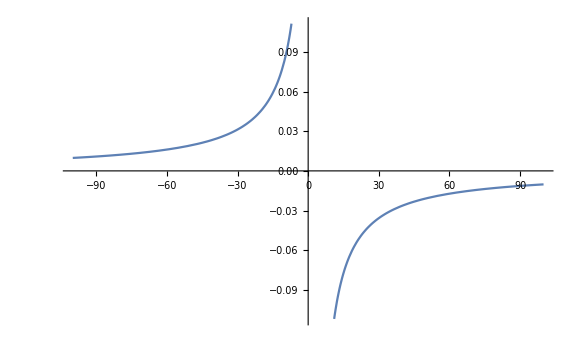

```mathematica
Plot[(Sqrt[(s-4)/s]-1)/(Sqrt[(s-4)/s]+1),{s,-100,100}]
```